## B - spline

```mathematica
Subscript[P, 0] = {{0},{0}};
(*Subscript[P, 1] = {{0.5},{0.5}};*)
Subscript[P, 1]= {Sqrt[(0-1)^2]/2,Sqrt[(0-53)^2]/2};
Subscript[P, 2] = {{1},{53}};
Subscript[Q, 0] = Subscript[P, 2];
Subscript[Q, 2]= {{80},{-32}};
```

### Parametrico

```mathematica
Subscript[P, i_] := {{Subscript[a, i]},{Subscript[b, i]}}
```

```mathematica
Subscript[Q, i_] := {{Subscript[c, i]},{Subscript[d, i]}}
```

```mathematica
Subscript[P, 1]
```

{1/2,53/2}

```mathematica
Subscript[P, 2]
```

{{1},{53}}

```mathematica
Subscript[B, 1]= Binomial[2,0]*Subscript[P, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[P, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[P, 2]*(1-l)^0*l^2
```

{{(1-l) l+l^2},{53 (1-l) l+53 l^2}}

```mathematica
Subscript[B, 2]= Binomial[2,0]*Subscript[Q, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[Q, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[Q, 2]*(1-l)^0*l^2
```

{{(1-l)^2+80 l^2+2 (1-l) l c_1},{53 (1-l)^2-32 l^2+2 (1-l) l d_1}}

```mathematica
Subscript[dB, 1] = D[Subscript[B, 1],l]
```

{{1},{53 (1-l)+53 l}}

```mathematica
Subscript[dB, 2] = D[Subscript[B, 2],l]
```

{{-2 (1-l)+160 l+2 (1-l) c_1-2 l c_1},{-106 (1-l)-64 l+2 (1-l) d_1-2 l d_1}}

```mathematica
eq = Flatten[(Subscript[dB, 1]/.l-> 1)] - Flatten[(Subscript[dB, 2]/.l-> 0) ]
```

{3-2 c_1,159-2 d_1}

```mathematica
sol = Solve[eq == 0]
```

{{c_1→3/2,d_1→159/2}}

```mathematica
Subscript[curva, 1] = Subscript[B, 1]
```

{{(1-l) l+l^2},{53 (1-l) l+53 l^2}}

```mathematica
Subscript[curva, 2] = Subscript[B, 2]/.sol
```

{{{(1-l)^2+3 (1-l) l+80 l^2},{53 (1-l)^2+159 (1-l) l-32 l^2}}}

```mathematica
(Subscript[B, 1]) // MatrixForm
```

((1-l) l+l^2
53 (1-l) l+53 l^2)

```mathematica
(Subscript[B, 2]) // MatrixForm
```

((1-l)^2+80 l^2+2 (1-l) l c_1
53 (1-l)^2-32 l^2+2 (1-l) l d_1)

```mathematica
Subscript[Q, 1]/.sol
```

{{{3/2},{159/2}}}

### Grafico

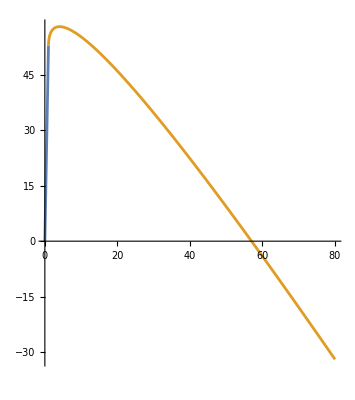

```mathematica
f[l_]:={{1. (1-l) l+l^2},{1. (1-l) l+2 l^2}};
f[l_] := Subscript[curva, 1]
f1[l_] := Subscript[curva, 2]
ParametricPlot[{f[l],f1[l]},{l,0,1}]
```

### Parametrico

```mathematica
Subscript[P, i_] := {{Subscript[a, i]},{Subscript[b, i]}}
```

```mathematica
Subscript[Q, i_] := {{Subscript[c, i]},{Subscript[d, i]}}
```

```mathematica
Subscript[P, 1]
```

{1/2,53/2}

```mathematica
Subscript[P, 2]
```

{{1},{53}}

```mathematica
Subscript[B, 1]= Binomial[2,0]*Subscript[P, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[P, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[P, 2]*(1-l)^0*l^2
```

{{(1-l) l+l^2},{53 (1-l) l+53 l^2}}

```mathematica
Subscript[B, 2]= Binomial[2,0]*Subscript[Q, 0]*(1-l)^2*l^0+Binomial[2,1]*Subscript[Q, 1]*(1-l)^1*l^1+Binomial[2,2]*Subscript[Q, 2]*(1-l)^0*l^2
```

{{(1-l)^2+80 l^2+2 (1-l) l c_1},{53 (1-l)^2-32 l^2+2 (1-l) l d_1}}

```mathematica
Subscript[dB, 1] = D[Subscript[B, 1],l]
```

{{1},{53 (1-l)+53 l}}

```mathematica
Subscript[dB, 2] = D[Subscript[B, 2],l]
```

{{-2 (1-l)+160 l+2 (1-l) c_1-2 l c_1},{-106 (1-l)-64 l+2 (1-l) d_1-2 l d_1}}

```mathematica
eq = Flatten[(Subscript[dB, 1]/.l-> 1)] - Flatten[(Subscript[dB, 2]/.l-> 0) ]
```

{3-2 c_1,159-2 d_1}

```mathematica
sol = Solve[eq == 0]
```

{{c_1→3/2,d_1→159/2}}

```mathematica
Subscript[curva, 1] = Subscript[B, 1]
```

{{(1-l) l+l^2},{53 (1-l) l+53 l^2}}

```mathematica
Subscript[curva, 2] = Subscript[B, 2]/.sol
```

{{{(1-l)^2+3 (1-l) l+80 l^2},{53 (1-l)^2+159 (1-l) l-32 l^2}}}

```mathematica
(Subscript[B, 1]) // MatrixForm
```

((1-l) l+l^2
53 (1-l) l+53 l^2)

```mathematica
(Subscript[B, 2]) // MatrixForm
```

((1-l)^2+80 l^2+2 (1-l) l c_1
53 (1-l)^2-32 l^2+2 (1-l) l d_1)

```mathematica
Subscript[Q, 1]/.sol
```

{{{3/2},{159/2}}}